# Thesis Plots

## Intialisation

```mathematica
setChapDir[name_]:=SetDirectory[FileNameJoin[{NotebookDirectory[],"Figures",name,"PlotData"}]]
Needs["ErrorBarPlots`"]
SetOptions[ListPlot,BaseStyle->{FontFamily->"Helvetica",FontSize->16,FontColor->Black},ImageSize->600,Frame->True,Axes->False];
SetOptions[Plot,BaseStyle->{FontFamily->"Helvetica",FontSize->16},ImageSize->600,Frame->True,Axes->False];
SetOptions[Histogram,BaseStyle->{FontFamily->"Helvetica",FontSize->16},ImageSize->600,Frame->True,Axes->False];
SetOptions[DateListPlot,BaseStyle->{FontFamily->"Helvetica",FontSize->16},ImageSize->600,Frame->True,Axes->False];
SetOptions[ErrorListPlot,BaseStyle->{FontFamily->"Helvetica",FontSize->16},ImageSize->600,Frame->True,Axes->False];
absq[z_]:=ComplexExpand[z Conjugate[z]]
```

myGridDivision can be used to set some kind of style for major and minor grids

```mathematica
myGridDivision[{min_,max_},{major_,majorStyle_},{minor_,minorStyle_}]:=Function[divisions,Join[{#,majorStyle}&/@divisions[[1]],{#,minorStyle}&/@Complement[Flatten[#[[2]]],#[[1]]]&@divisions]][FindDivisions[{min,max},{major,minor}]]
Colours=Darker[#]&/@{Red,Green,Blue,Black,Purple,Yellow,Brown,Orange,Pink,Gray,Cyan,Magenta};
```

```mathematica
plotExport[plot_,name_]:=Export["../"<>name<>".pdf",plot]
dataExport[plot_,name_]:=Module[{data},
data=Cases[plot,Line[data_]:>data,-4,1][[1]];
Export["../"<>name<>".txt",data,"Table"]
]
```

## Chapter 1

## Chapter 2

## Chapter 3

This section focuses on the experimental setup

```mathematica
setChapDir["Chapter3"]
```

/media/Storage/Dropbox/PhDWork/Thesis/Figures/Chapter3/PlotData

## Muquans Spectra

### Sat. Spec Signal

```mathematica
satspec = Import["satspec.csv"];
```

The 3,4 Rb85 crossover is at 384.2291813694837 THz. All frequencies will be shifted relative to that, in units of MHz

```mathematica
satdata={(#⟦1⟧-384.2291813694837)*10^6,#⟦2⟧+1.18}&/@satspec;
```

```mathematica
satspecPlot=ListPlot[satdata,GridLines->{myGridDivision[{-1500,1000},{5,GrayLevel[.1]},{10,{Dashed,GrayLevel[.8]}}],myGridDivision[{-2,4},{10,GrayLevel[.1]},{10,{Dashed,GrayLevel[.8]}}]},FrameStyle->Thick,FrameLabel->{"Detuning from^85Rb F=3 → F'=3,4 crossover (MHz)","abs. signal (arb. units)"}]
```

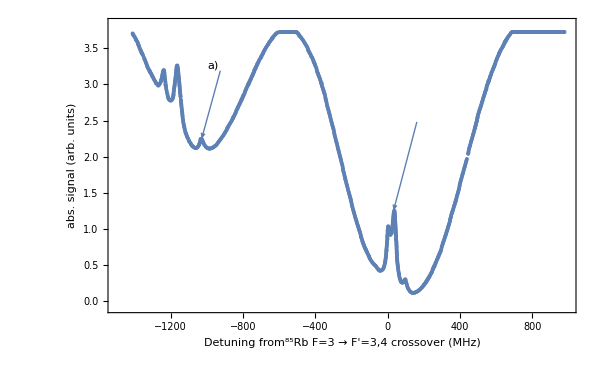

```mathematica
plotExport[satspecPlot,"sat_spec"]
```

### Error Signal

### Slave 0 Error

### Slave 1 Error

## Chapter 4 - MOT

## Chapter 5 - State Prep

## Chapter 6 - Interferometer

```mathematica
SetDirectory["~/Dropbox/PhDWork/Thesis/Figures/Chapter6"]
```

/media/Storage/Dropbox/PhDWork/Thesis/Figures/Chapter6

Key Functions

These functions are used to define the propagator for a two-level atom. This is a simplified model for the Raman transition

```mathematica
a[Ω_,δ_]:=√(Ω^2+δ^2)
prop[ω_,t_,a_,Ω_,ϕ_,δ_]:=({{ⅇ^(ⅈ (ω t)/2)( Cos[1/2 t a]-ⅈ δ/a Sin[1/2 t a]), - ⅇ^(ⅈ(ω t)/2)(ⅈ Ω ⅇ^(ⅈ ϕ)Sin[1/2 t a])/a}, {-ⅇ^(-ⅈ (ω t)/2)(ⅈ Ω ⅇ^(-ⅈ ϕ)Sin[1/2 t a])/a, ⅇ^(-ⅈ (ω t)/2)( Cos[1/2 t a]+ ⅈ δ/a Sin[1/2 t a])}})
prop[ω0_,ω_,δDopp_,Ω_,t0_,τ_,ϕ_]:=prop[ω+δDopp,τ,a[Ω,ω+δDopp-ω0],Ω,ϕ+ ω t0,ω-ω0+δDopp]
free[ω0_,T_]:={{ⅇ^(ⅈ ω0 T/2),0},{0,ⅇ^(-ⅈ ω0 T/2)}}
```

The fringe is then obtained from successive products of this operator and the free evolution

```mathematica
fringe[{Ω1_,τ1_,δ1_,ϕ1_} ,{Ω2_,τ2_,δ2_,ϕ2_},{Ω3_,τ3_,δ3_,ϕ3_},T1_,T2_,init_:{1,0}]:=prop[ω0,ω,δ3,Ω3,T2+τ2+T1+τ1,τ3,ϕ3].free[ω0,T2].prop[ω0,ω,δ2,Ω2,T1+τ1,τ2,ϕ2].free[ω0,T1].prop[ω0,ω,δ1,Ω1,0,τ1,ϕ1].init
```

Raman Optics

## Fringe Contrast vs Beam Width

I’ll consider the effects of the beam width on the contrast by assuming a Gaussian distribution of atoms. The total contrast is a convolution of this with the fringe pattern for a single atom. Without loss of generality, I can set the peak intensity to give the correct pulse area.

```mathematica
Ω[r_,Ω0_:Ω0]:=Ω0 Exp[-2 r^2/r0^2]
transverseFringe[T_]=1/(√(2π)σ)Exp[-rinit^2/(2 σ^2)]absq[fringe[{Ω[rinit,π/2],1,0,0},{Ω[rinit+u T-1/2 g T^2,π],1,0,ϕ},{Ω[rinit+u T-g T^2,π/2],1,0,0},T,T]]⟦1⟧;
```

```mathematica
contrast[cloud_,beam_]:=NIntegrate[Subtract@@(transverseFringe[25 10^-3]//.{ϕ->{0,π/2},u->0,ω->ω0,ω0->0,g->9.81,r0-> beam 10^-3,σ-> cloud 10^-3,rinit->r}),{r,-0.1,0.1},Method->"Trapezoidal"]
```

NIntegrate::inumri: The integrand -100 «2» (Cos[1/4 Power[«2»] π]^2 Cos[1/2 Power[«2»] π]^2 Cos[1/4 Power[«2»] π]^2+1. Cos[1/4 Power[«2»] π]^2 Sin[1/4 Power[«2»] π]^2 Sin[1/2 Power[«2»] π]^2-(«1»)/(«1»)-(«1»)/(«1»)+1. Cos[1/2 «1» π]^2 Sin[«1»]^2 Sin[1/4 Power[«2»] π]^2+1. Cos[1/4 Power[«2»] π]^2 Sin[1/2 Power[«2»] π]^2 Sin[1/4 Power[«2»] π]^2)+«1» has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{-∞,∞}}.

NIntegrate::inumri: The integrand -79.7885 ⅇ^(-20000. r^2) (0.+«12»+(«24» «5» («1»)^2)/(√(0.+«1») √(«1») («1»))+(24.3523 ⅇ^(«1») Cos[1/2 Power[«2»]]^2 Sin[1/2 Power[«2»]]^2 Sin[1/2 Power[«2»]]^2)/((0.+Power[«2»] Power[«2»]) (0.+1/4 Power[«2»] Power[«2»])))+79.7885 ⅇ^(-20000. «1») (0.+«13») has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{-∞,∞}}.

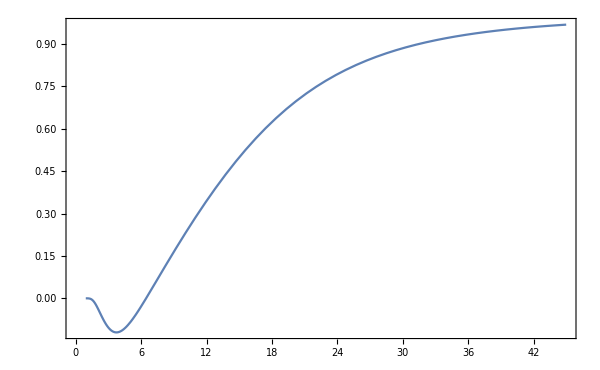

```mathematica
Plot[contrast[5,b],{b,0,45}]
```

```mathematica
dataExport[%82,"fringeContrast"]
```

../fringeContrast.txt

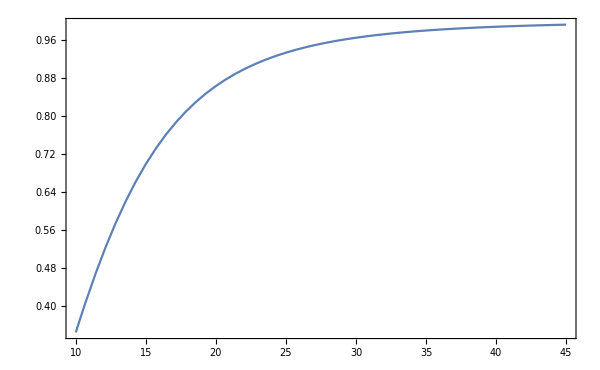

```mathematica
Plot[contrast[2.5,b],{b,10,45}]
```

## Phase Noise

Now I’ll consider the effects of phase noise on the fringe pattern. For this, I’ll generate fringes which have a random phase component at each pulse and take their average

```mathematica
absq[fringe[{1,π/2,0,ϕ1} ,{1,π,0,ϕ2},{1,π/2,0,ϕ3},T,T]//.{ω->0,ω0->0}]⟦1⟧//FullSimplify
```

Cos[1/2 (ϕ1-2 ϕ2+ϕ3)]^2

```mathematica
f[x_,n_]:=Mean[Cos[1/2 (ϕ1-2 ϕ2+ϕ3)]^2/.{ϕ1->RandomVariate[NormalDistribution[0,x],n],ϕ3->RandomVariate[NormalDistribution[0,x],n],ϕ2->ϕ2+RandomVariate[NormalDistribution[0,x],n]}]
```

```mathematica
a=;
```

```mathematica
a//FullSimplify
```

0.5+0.139463 Cos[2 ϕ2]+0.0233428 Cos[ϕ2] Sin[ϕ2]

```mathematica
Plot[Mean[Table[MaxValue[#,ϕ2]-MinValue[#,ϕ2]&[f[2 π/10,200]],{x,0,20,1}]]
```

0.304738

```mathematica
Plot[a,{ϕ2,-π,π}]
```

$Aborted

```mathematica
Plot[Evaluate[f[2 π/10,20000]],{ϕ2,-π,π}]
```

$Aborted

```mathematica
?RandomSample
```

RandomSample[{e_1,e_2,…},n] gives a pseudorandom sample of n of the e_i.
RandomSample[{w_1,w_2,…}→{e_1,e_2,…},n] gives a pseudorandom sample of n of the e_i chosen using weights w_i.
RandomSample[{e_1,e_2,…}] gives a pseudorandom permutation of the e_i.